# Gravitation

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 11/13/2024

## Readings

Explore these concepts using Wikipedia or your favorite mechanics textbook:
Gravitation, Escape velocity, Kepler’s Laws, Hohmann transfer orbit.

### Kepler’s Laws

Johannes Kepler, using Tycho Brahe and others’ observational data, could formulate three laws that are known as Kepler’s laws for planetary motion:
1. The orbit of each planet is an ellipse, where the Sun sits at one of the focal points.
2. The rate of sweeping the area by the imaginary line connecting the planet and the Sun is constant.
3. The orbital period squared is proportional to semi-major axis cubed.

Using these empirical laws as given facts, Isaac Newton came up with the Newton’s law of gravitation, which states that the gravitational force acting between a planet and its Sun is proportional to 1/r^2, where r is the distance between the centers of mass of these two objects.

### Gravitation, Force & Energy

More specifically, Newton’s law of Universal Gravitation tells us that the gravitational attraction between two masses, m and M, is of magnitude:
(1)	F = GmM/r^2,
where G = 6.67 ×10^-11Nm^2 kg^-2 (the gravitational constant), and r is their radial separation. The direction of the force is towards the other mass (radial and attractive).
The potential energy, U, of mass m due to the gravitational attraction of M is given by:
(2)	U = −GmM/r

If the orbit is circular, the relationship between the speed of m about M and the distance r between m and M can be easily derived from the Newton’s second law:
(3)	F =GmM/r^2 = ma = mv^2/r;
(4)	v^2r = GM.

Using this gravitational force one can solve the equation of motion and find that in a general case the orbits can be any one of the conic sections, i.e. circle, ellipse, parabola, or hyperbola. Thus, the two body problem, subject to a 1/r^2 force acting between them, is exactly solvable and always has an analytical solution.

Although the two-body problem is analytically solvable, adding a third body to the problem makes it impossible to solve analytically, although all the interactions in such a three-body system are still described by the Newton’s gravitational force. Three- (or more) body problem becomes chaotic. You can explore three-body or more complicated classical gravitational problems using simulation techniques similar to those we will be using in this lab.

## Procedure

Warnings:
- After opening this nb file run the Simulation Cells (denoted by orange bars) to avoid running through graphic boxes full of errors.
- NDSolveValue might give you an accuracy warning. You can safely ignore it.
- If the “Dynamic Updating” crashes and does not let you to use the Manipulation, reset it. See Evaluation > Dynamic Upgrading Enabled option from the top menu. Uncheck-mark and check-mark this option, or click on Abort on the pop-up message and go and check-mark the option.
- For the escape velocity section, if the simulation is taking too long you can use Evaluation > Abort Evaluation from the top menu or press Alt+. shortcut key. Then try to set the initial conditions in a way that the orbit is on a line (not a parabola or hyperbola), or decrease the running time tmax1, and run again.

This lab will have three parts. As it is almost impossible to freely do gravitational force experiments and hard to explore the actual astronomical data, we will gather our own data by solving the F = ma equations and will assume that all the masses involved interact via the Newtonian gravity. Here, we will call these numerical solutions, simulations.

All the simulations in this lab will use NDSolveValue command to solve the differential equation based on F= ma numerically. The only parameters that you will need to vary are the initial conditions and, perhaps, tmax variable (highlighted light-red inside the simulation cells). You will set the initial conditions for the mass m, and we will assume that m << M and M stays put (fixed in space). We take M to represent the Earth, and m to represent a small object (like a satellite or an asteroid) with a mass of m = 100 kg.

There are quite a few parameters involved in this lab. Instead of using numerical values, use G, R, M, m, ... variables inside Input cells that you use to do the calculations. This will make your calculations and report much more readable. 

Also please do not copy the simulation code cells as it will make reading the report much harder. There are only few lines of code which you might need to add to do certain plotting or calculations. Only edit the simulation cells as you see fit and avoid copy&pasting.

In part I, you will explore the impact velocity and also the escape velocity. You will do a prediction first and then simulate and see if you can verify your predictions.

In part II, you will review the circular orbit and predict the velocity needed to have a circular orbit, to be checked with simulations.

In part III, we will verify the Kepler’s 1st and 3rd laws using simulations.

## Dialog:

## Part I. Impact & Escape Velocity

### Step 1. Impact Velocity

- Explore the simulation code below. Click on the small plus button by the slider for t (time) and play the simulation. Explore the functionality of the slider.
- Now change the initial conditions x[0], y[0], x’[0], and y’[0] inside the NDSolveValue command below and see how it affects the simulation. You can also change the tmax1 variable which shows how long the simulation will run (if there is no impact). These lines are highlighted on the code below.

### Simulation Cell 1

```mathematica
(* --- The chunk of code C1 begins. --- *)
PE[x_, y_] = -G M m/(x^2+y^2)^(1/2);
KE[vx_, vy_] = (1/2)m(vx^2 + vy^2);
Energy[x_, y_, vx_, vy_] = PE[x, y] + KE[vx, vy];
(* End of chunk C1. *)

(* --- The chunk of code C2 begins. --- *)
G=6.672*10^-11; (* Gravitational constant in m^3 kg^-1 s^-2. *)
M=5.972*10^24; (* Mass of Earth in kg. *)
m = 100; (* Mass of the object in kg. *)
R=6.371*10^6; (* Earth mean radius in m. *)
(* End of chunk C2. *)

(* --- The chunk of code C3 begins. --- *)
tmax1=100000; (* Max1mum running time *)
(* Below we are solving the equations of motion for an object much smaller than Earth in Earth's gravitational field with given initial conditions. *)
(* x1 and y1 are the solutions for the position of the object. i stands for part i. *)
{x1,y1}=NDSolveValue[{
x''[t]==-((G M x[t])/(x[t]^2+y[t]^2)^(3/2)),
y''[t]==-((G M y[t])/(x[t]^2+y[t]^2)^(3/2)),
x[0]==3R,
y[0]==0,
x'[0]==0,
y'[0]==4565.869436434148,
WhenEvent[x[t]^2+y[t]^2-R^2<0,{tmax1=t, "StopIntegration"}]},
{x,y},{t,0,tmax1},MaxSteps->10000000];
(* End of chunk C3. *)

(* Below we are using Manipulate command with an interactive slider t to change the time and have an interactive simulation. *)
Manipulate[
Grid[{
{Show[
Graphics[{LightBlue,Disk[{0,0},R]},ImageSize->Large, PlotRange->All,PlotRangePadding->Scaled[.15]], (* Drawing a Disk for Earth *)
Graphics[{PointSize[.025],Hue[0],Point[{x1[t],y1[t]}]}],(* Drawing a Point for the object. *)
ParametricPlot[{x1[t],y1[t]},{t,0,tmax1},AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large,Axes->True] (* Plotting the path. *)
],
Grid[{
{Text["TABLE X11. Measurements"],SpanFromLeft},
{"Time, s","r, m", "v, m/s", "a, m/s^2","K.E., J","P.E., J","E, J"},
{t, Sqrt[x1[t]^2+y1[t]^2], Sqrt[x1'[t]^2+y1'[t]^2], Sqrt[x1''[t]^2+y1''[t]^2], KE[x1'[t],y1'[t]],PE[x1[t],y1[t]],Energy[x1[t],y1[t],x1'[t],y1'[t]]},
{Text["TABLE X12. xy Notation Variables"],SpanFromLeft},
{"Time, s","x, m", "y, m", "v_x, m/s","v_y, m/s","a_x, m/s^2","a_y, m/s^2"},
{t, x1[t], y1[t],x1'[t], y1'[t], x1''[t], y1''[t]}
},Frame->All]
}
}],
{t,0,tmax1,Appearance->"Labeled"}]
```

#### Question 1. - Briefly explain what each of the chunks C1, C2, and C3 does on the above code. C1 defines functions that calculate the energy of the little mass (Kinetic), Potential energy of the system as well as the total energy of the system (Sum of Kinetic and Potential). C2 defines the constants like mass, Radius of planet, Universal Gravitational Constant, etc. C3 defines initial conditions for dynamic parameters like position and velocity.

#### Question 2. - Give an example of the initial conditions, at which the object would move along a straight line before the impact. x[0] == 6 R, y[0] == 0, x’[0] == 0, y’[0] == 0 These parameters imply that there is no initial bias in the object’s movement. The only thing changing the object’s position is gravity which always acts on the same radial line.

#### Question 3. - What can you conclude about the total energy during the fall? The total energy of the system does not change. (The only forces acting here are conservative, sum of K and U is constant (E)). - Considering the impact is totally inelastic, which variable above shows the energy released by the mass m when hitting the Earth? Kinetic Energy (KE) would drop to zero upon an inelastic collision. - What is the acceleration of mass m when hitting the Earth? The acceleration at that point is about -9.81659 (g!).

#### Question 4. - Use the initial condition, x(0) = 3.0 R, y(0) = 4.0 R, v_x(0) = 2.0 km/s, v_y(0) = 1.5 km/s, and theoretically calculate the magnitude of the impact velocity. Show your work. (Use G, R, and other variables defined above. Show your derivation using analytical expressions first, without plugging in the numbers. Then, plug in the above four initial conditions to get the final numerical answer for the impact velocity.) The initial Energy (Given by 1/2mv0^2 + GMm/r0) is -9.3833×10^8 The final Potential Energy (At radial distance R since that is where the mass impacts) is -6.25415×10^9 Hence the Final Kinetic Energy, by conservation of energy would be E_i - U_f = 5.31582×10^9 Since that is equal to 1/2mv_impact^2, v_impact = 10311 m/s^2 - Simulate this initial condition on above simulation code and check your answer. The simulation also says that the impact velocity is 10311 m/s^2

```mathematica
InitialEnergyQ4 = PE[3R, 4R]+KE[2000, 1500]
FinalPotentialEQ4 = PE[R, 0]
FinalKEQ4 = InitialEnergyQ4 - FinalPotentialEQ4 (*1/2mv^2 ⇒ v = Sqrt[2*FinalKEQ4/m]*)
vImpactQ4 = Sqrt[2*FinalKEQ4/m]
```

-9.3833×10^8

-6.25415×10^9

5.31582×10^9

10311.

### Step 2. Escape Velocity

Now we want to set the initial conditions on the above simulation so that the mass m escapes from the gravitational field of the Earth.
- Before doing the simulations, fill out Table 1A below that gives your predictions for the escape velocity at different initial radial distances, to escape the gravitational field of the Earth.

```mathematica
Grid[{{Text["TABLE 1A. Escape Velocity, Theoretical Calculations"],SpanFromLeft},
{"r(t=0)","v_(ESCAPE, TH) (m/s)"},{"1.00 R",Sqrt[2G M /R]},{"3.00 R",Sqrt[2G M /(3R)]}, {"9.00 R", Sqrt[2G M /(9R)]}},Frame->All]
```

TABLE 1A. Escape Velocity, Theoretical Calculations | 
r(t=0) | v_(ESCAPE, TH) (m/s)
1.00 R | 11184.1
3.00 R | 6457.11
9.00 R | 3728.02

- Now use simulations and fill out Table 1B below. You only need to estimate the v_ESCAPE by 5% error margin using the simulation above. Take the theoretical values and observe what happens with slightly smaller or greater initial velocities.
Do not copy the simulation code, as it will make your report untidy. Just edit and run the same simulation above.

Grid[{{Text["TABLE 1B. Escape Velocity, Using Simulations"],SpanFromLeft},
{"r(t=0)","v_(ESCAPE, SIM) (m/s)"},{"1.00 R",11184.050351432657},{"3.00 R",6457.114481029973}, {"9.00 R", 3728.0167838108855}},Frame→All]


Error (1R): 9.53674×10^-7
Error (3R): 2.38419×10^-7
(The Program was always unresponsive for values of v around 9R)

TABLE 1B. Escape Velocity, Using Simulations | 
r(t=0) | v_(ESCAPE, SIM) (m/s)
1.00 R | 11184.1
3.00 R | 6457.11
9.00 R | 3728.02

Obviously we can not sun the simulation for infinite time. We can however, compare the energies of the object for our initial conditions. If the Total energy is almost zero, then the object’s velocity is the escape velocity.

For the theoretically calculated velocities, all of them result in zero total velocity of the object (The kinetic energy being almost sufficient enough to overcome the Potential Energy of the mass.)
The error of the energy is the deviation from zero wrt the Potential Energy of the System. For me, all errors were less than 0.01%, let alone 5%.

Increasing the velocity further from the theoretical escape velocity would cause a positive deviation in energy. Decreasing the velocity would cause a negative deviation in the total energy.

#### Question 5. - Is the direction of the initial escape velocity important? How? Explore using the simulation. The direction of the initial velocity does not matter. Each direction you point it to results to the escape of the object since the object would have enough kinetic energy to overcome the gravitational potential energy (thus fly off past infinity beyond the influence of gravity). (even pointing it to the center would make it escape since even though you gain potential energy, you also gain enough kinetic energy to overcome that potential energy that you gain in moving inside at first.)

## Part II. Circular Orbits

The circular orbits are easy to study analytically, compared to elliptic, parabolic, or hyperbolic orbits. The green circle on the simulation is a circle as a guide.
- Theoretically determine the initial conditions for velocity to get a circular orbit with a radius r = 3.00 R and record on the table below.
- Set this initial condition on the simulation below to check your answer. Determine the ‘maximum radius minus minimum radius’ divided by r(0) = 3.00 R.
(Hint: To find this value an easy way is to plot (r(t))/(r(0))-1 as a function of time and record the peak-to-peak value (for the vertical axis).
The code for this plot is given below.)

Answer
4565.87 m/s is the Orbital velocity of the Object to Revolve around Earth in a Stable Orbit of Radius 3R. This also checks out with the simulation (at least for time t=100000, the simulation breaks for time of higher orders.)

```mathematica
vOrbitalP2 = Sqrt[G M/(3R)]
```

4565.87

```mathematica
Grid[{{Text["TABLE 2. Circular Orbit Parameters"],SpanFromLeft},
{"r(0)","theoretical v(0)","(max r  -  min r)/(r (0)) in simulation"},
{"3.00 R", 4565.87, 0.498+1.16*10^(-4)}
},Frame->All]
```

TABLE 2. Circular Orbit Parameters |  | 
r(0) | theoretical v(0) | (max r  -  min r)/(r (0)) in simulation
3.00 R | 4565.87 | 0.498116

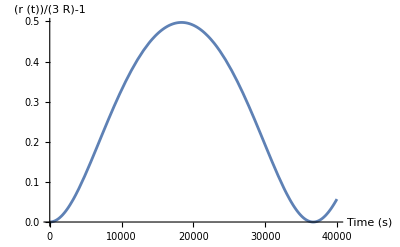

```mathematica
Plot[{Sqrt[x2[t]^2+y2[t]^2]/(3R) - 1},{t,0,tmax2},AxesLabel->{"Time (s)", "(r (t))/(3  R)-1"}]
```

#### Question 1. - Describe how the angle between the velocity and acceleration vectors changes with time and how this is related to the fact that both potential and kinetic energy remain constant. The angle between velocity and acceleration is almost 90° over time. This means that there is no change in the magnitude of the velocity vector but only a change in the direction of the velocity vector. (Since the magnitude doesn’t change, the Kinetic Energy doesn’t change, and Hence the Work done by gravity is Zero. Hence the change in potential energy would also be zero.) Therefore, a perpendicular angle between velocity and acceleration means a constant potential and kinetic energy.

### Simulation Cell 2

```mathematica
(* --- The chunk of code C1 begins. --- *)
PE[x_, y_] = -G M m/(x^2+y^2)^(1/2);
KE[vx_, vy_] = (1/2)m(vx^2 + vy^2);
Energy[x_, y_, vx_, vy_] = PE[x, y] + KE[vx, vy];
(* End of chunk C1. *)

(* --- The chunk of code C2 begins. --- *)
G=6.672*10^-11; (* Gravitational constant in m^3 kg^-1 s^-2. *)
M=5.972*10^24; (* Mass of Earth in kg. *)
m = 100; (* Mass of the object in kg. *)
R=6.371*10^6; (* Earth mean radius in m. *)
(* End of chunk C2. *)

(* --- The chunk of code C3 begins. --- *)
tmax2=40000;  (* Max1mum running time *)
(* Below we are solving the equations of motion for an object much smaller than Earth in Earth's gravitational field with given initial conditions. *)
(* x2 and y2 are the solutions for the position of the object. ii stands for part ii. *)
{x2,y2}=NDSolveValue[{
x''[t]==-((G M x[t])/(x[t]^2+y[t]^2)^(3/2)),
y''[t]==-((G M y[t])/(x[t]^2+y[t]^2)^(3/2)),
(* Set the initial conditions based on your calculations to get a circular motion. *)
x[0]==0,
y[0]==3R,
x'[0]==4565.87, 
y'[0]==0,
WhenEvent[x[t]^2+y[t]^2-R^2<0,{tmax2=t, "StopIntegration"}]},
{x,y},{t,0,tmax2},MaxSteps->10000000];
(* End of chunk C3. *)

scaleAccPos = Abs[x2[tmax2/2]/(Sqrt[x2''[tmax2/2]^2+y2''[tmax2/2]^2])] ; (* How big the acceleration vector shown on position graph. *)
scaleVelPos= Abs[x2[tmax2/2]/(Sqrt[x2'[tmax2/2]^2+y2'[tmax2/2]^2])]; (* How big the velocity vector shown on position graph. *)

(* Below we are using Manipulate command with an interactive slider t to change the time and have an interactive simulation. *)
Manipulate[
Grid[
{
{Show[
ParametricPlot[{x2[t],y2[t]},{t,0,tmax2},AxesLabel->{"x","y"},PlotStyle->Automatic,PlotRange->Full,ImageSize->Large],
Graphics[{LightBlue,Disk[{0,0},R]},ImageSize->Large, PlotRange->All],
Graphics[{Green, Circle[{0,0}, 3R]}], (* A Green Circle at r=3R as a guide. *)
Graphics[{PointSize[.025],Hue[0],Point[{x2[t],y2[t]}]}],
Graphics[{Black,Arrow[{{x2[t],y2[t]},{x2[t]+scaleAccPos x2''[t],y2[t]+scaleAccPos y2''[t]}}]}],
Graphics[{Red,Arrow[{{x2[t],y2[t]},{x2[t]+scaleVelPos x2'[t],y2[t]+scaleVelPos y2'[t]}}]}]
],
Grid[{
{Text["TABLE X21. Measurements"],SpanFromLeft},
{"Time, s","r, m", "v, m/s", "a, m/s^2","K.E., J","P.E., J","E, J"},
{t, Sqrt[x2[t]^2+y2[t]^2], Sqrt[x2'[t]^2+y2'[t]^2], Sqrt[x2''[t]^2+y2''[t]^2], KE[x2'[t],y2'[t]],PE[x2[t],y2[t]],Energy[x2[t],y2[t],x2'[t],y2'[t]]},
{Text["TABLE X22. xy Notation Variables"],SpanFromLeft},
{"Time, s","x, m", "y, m", "v_x, m/s","v_y, m/s","a_x, m/s^2","a_y, m/s^2"},
{t, x2[t], y2[t],x2'[t], y2'[t], x2''[t], y2''[t]}
},Frame->All]
},
{Show[
Plot[{PE[x2[t],y2[t]], KE[x2'[t],y2'[t]],Energy[x2[t],y2[t],x2'[t],y2'[t]]},{t,0,tmax2},ImageSize->Large,PlotRange->All, PlotLegends->{"PE", "KE", "E"}, AxesLabel->{"Time (s)", ""}],
Graphics[{PointSize[.025],Hue[0],Point[{t,PE[x2[t],y2[t]]}]}],
Graphics[{PointSize[.025],Hue[0],Point[{t,KE[x2'[t],y2'[t]]}]}],
Graphics[{PointSize[.025],Hue[0],Point[{t,Energy[x2[t],y2[t],x2'[t],y2'[t]]}]}]],
Show[
Graphics[{PointSize[0.015],Opacity[0.5],Point[{0,0}]}, AxesLabel->{Subscript["v","x"],Subscript["v","y"]},Axes->True, ImageSize->Large],
ParametricPlot[{x2'[t],y2'[t]},{t,0,tmax2},AxesLabel->{Subscript["v","x"],Subscript["v","y"]},Axes->True,PlotStyle->Automatic,PlotRange->Full,ImageSize->Large],
Graphics[{PointSize[.025],Hue[0],Point[{x2'[t],y2'[t]}]}, ImageSize->Large],
Graphics[{Red,Arrow[{{0,0},{x2'[t],y2'[t]}}]}]
]
}
}],{t,0,tmax2,Appearance->"Labeled"}]
```

## Part III. Kepler's Laws

### Step 1. Kepler's First Law:

In this part we will study the elliptic orbits. Using the simulation we will determine the distances of apocenter (furthest recession) R_a, and pericenter (closest approach) R_p. The corresponding terms for motion around the sun are aphelion and perihelion and for motion about the earth, perigee and apogee.
Note that R_a and R_p are magnitudes, i.e. always positive. The semi-major axis length of the ellipse is a and e is the eccentricity which can be defined for an ellipse as,
R_p/R_a=(1-e)/(1+e),
 e=(R_a-R_p)/(R_a+R_p).
Here you will use the simulation to set the initial velocity. Then you will measure R_a and R_p using the simulation. Then you correct these parameters on the code which makes the green curve to be an ellipse with one focal point being M.
Again, the only lines you need or might need to change are highlighted by a light red color.

- First set the initial value of v_x(0) to the value you calculated for a circular orbit and run the simulation to confirm your result. Fill out the table below.
Correct the Ellipse Parameters on the simulation code below and run it again. Notice if the Green ellipse is a good fit to for the orbit.

- Now set the initial velocity v_x(0) to 90% of the escape velocity for r(0) = 3R. Fill out the table below.
Correct the Ellipse Parameters on the simulation code below and run it again. Notice if the Green ellipse is a good fit to for the orbit.

- Now set the initial velocity v_x(0) so that in the simulation you get the perigee point to be fairly close to the surface of the Earth. Fill out the table below.
Correct the Ellipse Parameters on the simulation code below and run it again. Notice if the Green ellipse is a good fit to for the orbit.

```mathematica
vx1 = 4565.87;
Ra1 = 3R;
Rp1 = 3R;
vx2 = 0.9*vx1;
Ra2 = 1.3*10^7;
Rp2 = 3R;
vx3 = 0.72*vx1;
Ra3 = 6.67*10^6;
Rp3 = 3R;
```

```mathematica
Grid[{{Text["TABLE 3A. Kepler's First Law"],SpanFromLeft},
{"v_x(0), m/s","R_a, m","R_p, m", "e (eccentricity)", "a (semi-major axis), m"},
{vx1,Ra1,Rp1,0,1.9113*10^7},{vx2,Ra2,Rp2,0.19035904462367267,1.60565*10^7},{vx3,Ra3,Rp3,0.4826048171275647,1.28915*10^7}},Frame->All]
```

TABLE 3A. Kepler's First Law |  |  |  | 
v_x(0), m/s | R_a, m | R_p, m | e (eccentricity) | a (semi-major axis), m
4565.87 | 1.9113×10^7 | 1.9113×10^7 | 0 | 1.9113×10^7
4109.28 | 1.3×10^7 | 1.9113×10^7 | 0.190359 | 1.60565×10^7
3287.43 | 6.67×10^6 | 1.9113×10^7 | 0.482605 | 1.28915×10^7

#### Question 1. - Describe how the angle between the velocity and acceleration vectors changes with time. Explain why and how it differs from the case of a circular orbit and how the change in kinetic and potential energy is related to the angle. The angle between the velocity and acceleration now change. For the major axis, the velocities are perpendicular to the acceleration. The angles thereafter become obtuse since it is an ellipse now. As the angles change, the energy remains the same but its distribution as Kinetic or Potential energy varies, unlike a circular motion. In this case, when the orbiting object is closer to the planet, it has higher kinetic energy and also lower potential energy. As it moves further away, the positions swap. I.e., the kinetic energies oscillate in a cycle of every 2 times the angles are pi/2 (once during closest approach and once during furthest approach).

#### Question 2. - The Green ellipse drawn on the simulation is a perfect theoretical ellipse with the center of Earth sitting at one of its focal points. What can you conclude about Kepler’s first law? Keplar’s first law states that planets orbit the sun in perfect ellipses with sun at one of the focal centres. Our simulation works exactly as Kepler described motion of objects under the influence of gravity, hence, we can conclude Kepler’s first law is correct.

### Simulation Cell 3

```mathematica
(* --- The chunk of code C1 begins. --- *)
PE[x_, y_] = -G M m/(x^2+y^2)^(1/2);
KE[vx_, vy_] = (1/2)m(vx^2 + vy^2);
Energy[x_, y_, vx_, vy_] = PE[x, y] + KE[vx, vy];
(* End of chunk C1. *)

(* --- The chunk of code C2 begins. --- *)
G=6.672*10^-11; (* Gravitational constant in m^3 kg^-1 s^-2. *)
M=5.972*10^24; (* Mass of Earth in kg. *)
m = 100; (* Mass of the object in kg. *)
R=6.371*10^6; (* Earth mean radius in m. *)
(* End of chunk C2. *)

(* --- The chunk of code C3 begins. --- *)
tmax3=400000;  (* Max1mum running time *)
(* Below we are solving the equations of motion for an object much smaller than Earth in Earth's gravitational field with given initial conditions. *)
(* x3 and y3 are the solutions for the position of the object. ii stands for part ii. *)
{x3,y3}=NDSolveValue[{
x''[t]==-((G M x[t])/(x[t]^2+y[t]^2)^(3/2)),
y''[t]==-((G M y[t])/(x[t]^2+y[t]^2)^(3/2)),
(* Set the initial conditions based on your calculations to get a circular motion. *)
x[0]==0,
y[0]==3R,
x'[0]==vx1, 
y'[0]==0,
WhenEvent[x[t]^2+y[t]^2-R^2<0,{tmax3=t, "StopIntegration"}]},
{x,y},{t,0,tmax3},MaxSteps->10000000];
(* End of chunk C3. *)

scaleAccPos = Abs[x3[tmax3/2]/(Sqrt[x3''[tmax3/2]^2+y3''[tmax3/2]^2])] ; (* How big the acceleration vector shown on position graph. *)
scaleVelPos= Abs[x3[tmax3/2]/(Sqrt[x3'[tmax3/2]^2+y3'[tmax3/2]^2])]; (* How big the velocity vector shown on position graph. *)

(* Ellipse Parameters *)
Ra=Ra1;
Rp =Rp1;
e=(Ra - Rp)/(Ra + Rp); (* e is the eccentricity, e=0 is a circle and e=1 is a parabola. *)
a=(Ra+Rp)/2; (* a is the semi-mojor axis. *)
B=a; (* The semi-major axis is in y direction. *)
A=Sqrt[Ra*Rp]; (* The semi-minor axis is in x direction. *)
(* ------------------ *)

(* Below we are using Manipulate command with an interactive slider t to change the time and have an interactive simulation. *)
Manipulate[
Grid[
{
{Show[
ParametricPlot[{x3[t],y3[t]},{t,0,tmax3},AxesLabel->{"x","y"},PlotStyle->Automatic,PlotRange->Full,ImageSize->Large],
Graphics[{LightBlue,Disk[{0,0},R]},ImageSize->Large, PlotRange->All],
Graphics[{Green, Circle[{0,-e*a},{A,B}]}], (* This line is drawing the theoretical ellipse to check Kepler's first law. *)
Graphics[{PointSize[.025],Hue[0],Point[{x3[t],y3[t]}]}],
Graphics[{Black,Arrow[{{x3[t],y3[t]},{x3[t]+scaleAccPos x3''[t],y3[t]+scaleAccPos y3''[t]}}]}],
Graphics[{Red,Arrow[{{x3[t],y3[t]},{x3[t]+scaleVelPos x3'[t],y3[t]+scaleVelPos y3'[t]}}]}]
],
Grid[{
{Text["TABLE X31. Measurements"],SpanFromLeft},
{"Time, s","r, m", "v, m/s", "a, m/s^2","K.E., J","P.E., J","E, J"},
{t, Sqrt[x3[t]^2+y3[t]^2], Sqrt[x3'[t]^2+y3'[t]^2], Sqrt[x3''[t]^2+y3''[t]^2], KE[x3'[t],y3'[t]],PE[x3[t],y3[t]],Energy[x3[t],y3[t],x3'[t],y3'[t]]},
{Text["TABLE X32. xy Notation Variables"],SpanFromLeft},
{"Time, s","x, m", "y, m", "v_x, m/s","v_y, m/s","a_x, m/s^2","a_y, m/s^2"},
{t, x3[t], y3[t],x3'[t], y3'[t], x3''[t], y3''[t]}
},Frame->All]
},
{Show[
Plot[{PE[x3[t],y3[t]], KE[x3'[t],y3'[t]],Energy[x3[t],y3[t],x3'[t],y3'[t]]},{t,0,tmax3},ImageSize->Large,PlotRange->All, PlotLegends->{"PE", "KE", "E"}, AxesLabel->{"Time (s)", ""}],
Graphics[{PointSize[.025],Hue[0],Point[{t,PE[x3[t],y3[t]]}]}],
Graphics[{PointSize[.025],Hue[0],Point[{t,KE[x3'[t],y3'[t]]}]}],
Graphics[{PointSize[.025],Hue[0],Point[{t,Energy[x3[t],y3[t],x3'[t],y3'[t]]}]}]],
Show[
Graphics[{PointSize[0.015],Opacity[0.5],Point[{0,0}]}, AxesLabel->{Subscript["v","x"],Subscript["v","y"]},Axes->True, ImageSize->Large],
ParametricPlot[{x3'[t],y3'[t]},{t,0,tmax3},AxesLabel->{Subscript["v","x"],Subscript["v","y"]},Axes->True,PlotStyle->Automatic,PlotRange->Full,ImageSize->Large],
Graphics[{PointSize[.025],Hue[0],Point[{x3'[t],y3'[t]}]}, ImageSize->Large],
Graphics[{Red,Arrow[{{0,0},{x3'[t],y3'[t]}}]}]
]
}
}],{t,0,tmax3,Appearance->"Labeled"}]
e
a
```

0.

1.9113×10^7

```mathematica
|
```

### Step 2. Kepler’s Third Law:

In this step, you will use at least four different data points using the simulation above. You can copy three columns from the table 3A and add another measurement. T is the period of the motion, i.e. the time it takes to complete one full turn on the orbit.

```mathematica
Grid[{{Text["TABLE 3B. Kepler's First Law"],SpanFromLeft},
{"v_x(0), m/s","R_a, m","R_p, m", "a, m" ,"T, s", "a^3, m^3", "T^2, s^2"},
{vx1,Ra1,Rp1,1.9113*10^7,26300, (1.9113*10^7)^3, 26300^2},
{vx2,Ra2,Rp2,1.60565*10^7,20250, (1.60565*10^7)^3, 20250^2},
{vx3,Ra3,Rp3,1.28915*10^7,14600, (1.28915*10^7)^3, 14600^2}
},Frame->All]
```

TABLE 3B. Kepler's First Law |  |  |  |  |  | 
v_x(0), m/s | R_a, m | R_p, m | a, m | T, s | a^3, m^3 | T^2, s^2
4565.87 | 1.9113×10^7 | 1.9113×10^7 | 1.9113×10^7 | 26300 | 6.98211×10^21 | 691690000
4109.28 | 1.3×10^7 | 1.9113×10^7 | 1.60565×10^7 | 20250 | 4.13955×10^21 | 410062500
3287.43 | 6.67×10^6 | 1.9113×10^7 | 1.28915×10^7 | 14600 | 2.14245×10^21 | 213160000

Now we will make a linear fit using the data gathered above for T^2 versus a^3 to check the Kepler’s third law.
- First find a theoretical value for the slope of the linear fit. In other words, if T^2/a^3 is independent of the shape of the ellipse, find it in terms of the known parameters of the motion, like G, M, m, and numerical constants.
- Now do a linear fit for the T2va3, we will use 0,0 as a theoretical data here! The column on the left is a^3 and it is the horizontal axis.

```mathematica
T2va3={{0, 0}, {26300.^2, (1.9113*10^7)^3}, {20250^2, (1.60565*10^7)^3}, {14600^2, (1.28915*10^7)^3}};
line=Fit[T2va3, {a3},a3]
Show[Plot[line,{a3,0,Max[T2va3[[All,1]]]}, AxesLabel->{"a^3 (m^3)","T^2 (s^2)"}],ListPlot[T2va3,PlotStyle->Red]]
```

1.00916×10^13 a3

-Graphics-

- Find the error of the slope above.
- Compare the theoretical value to the fit value you get from the simulation data.


The error for the fit turns out to be 1.01 * 10^-7
The theoretical values show a linear correlation between T^2 and a^3. That is what we see for the above plot. Hence,  Kepler’s 3rd law seems to be right as well.

Rutgers 275 Classical Physics Lab
“Gravitation”
Copyright 2016 Roshan Tourani and Girsh Blumberg ©